```mathematica
ysol1=NDSolve[{y''[x]+Exp[-2*(y[x])]==0,y[1]==0,y[2]==Log[2]},y,{x,1,2}]
```

{{y→InterpolatingFunction[…]}}

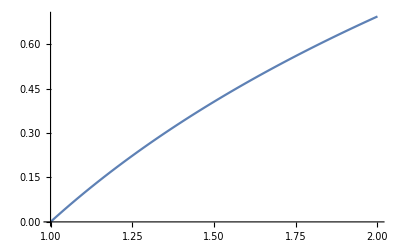

```mathematica
Plot[First[y[x]/.ysol1],{x,1,2}]
```

```mathematica
ysol2=NDSolve[{y''[x]-y'[x]*Cos[x]+y[x]*Log[y[x]] ==0,y[0]==1,y[π/2]==Exp[1]},y,{x,0,π/2}]
```

{{y→InterpolatingFunction[…]}}

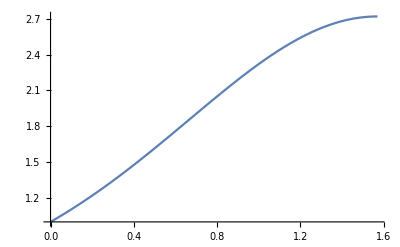

```mathematica
Plot[First[y[x]/.ysol2],{x,0,π/2}]
```

```mathematica
ysol3=NDSolve[{y''[x]+(2*(y'[x])^3+(y[x])^2*(y'[x]))*Sec[x]== 0,y[π/4]==2^(-(1/4)),y[π/3]==0.5*(12^(1/4))},y,{x,π/4,π/3}]
```

{{y→InterpolatingFunction[…]}}

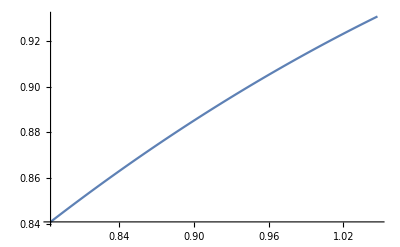

```mathematica
Plot[First[y[x]/.ysol3],{x,π/4,π/3}]
```

```mathematica
ysol4=NDSolve[{y''[x]+0.5*(y'[x])^(2) +0.5*y[x]*Sin[x]-0.5==0,y[0]==2,y[π]==2},y,{x,0,π}]
```

{{y→InterpolatingFunction[…]}}

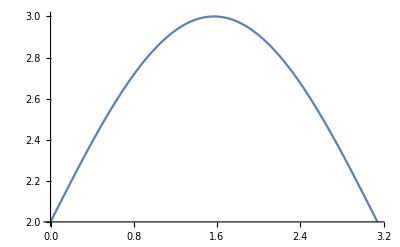

```mathematica
Plot[First[y[x]/.ysol4],{x,0,π}]
```